# Unidad 1 2 - Análisis de datos

En esta sección se verá un ejemplo de análisis de datos simple usando las funciones de ajuste de Mathematica.

## Resistencias en serie

Se trabajará sobre unas mediciones de laboratorio de la intensidad de corriente medida en un circuito con resistencias en serie haciendo variar el voltaje.

La relación entre intensidad y voltaje está dada por V = RI. Entonces despejando la intensidad queda I = V/R. En este experimento el valor de la resistencia total especificada por los fabricantes es R = 24910 Ω. Los datos medidos en el experimento son

Para comenzar el análisis se introducen los datos.

```mathematica
datos = {{3,111.3 10^-6},{6,2.31 10^-4},{9,3.47 10^-4},{12,4.62 10^-4},{15,5.79 10^-4},{18,6.96 10^-4},{21,8.13 10^-4},{24,9.30 10^-4},{27,1.05 10^-3},{30,1.16 10^-3}};
```

Es notable que todos los puntos parecen alinearse sobre una recta.

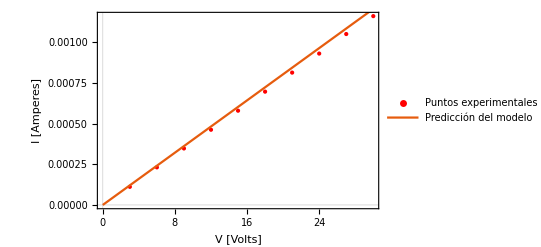

```mathematica
Show[
ListPlot[datos,PlotTheme->"Scientific",FrameLabel->{"V [Volts]","I [Amperes]"},BaseStyle->FontSize->15,PlotStyle->{Red,PointSize[Large]},PlotLegends->{"Puntos experimentales"}],
Plot[V/24910,{V,0,30},PlotTheme->"Scientific",PlotLegends->{"Predicción del modelo"}]
]
```

Con esto podemos tratar de realizar un ajuste lineal.

```mathematica
ajuste = Fit[datos,{1,V},V]
```

-3.94667×10^-6+0.0000389016 V

Se compara el modelo contra el ajuste

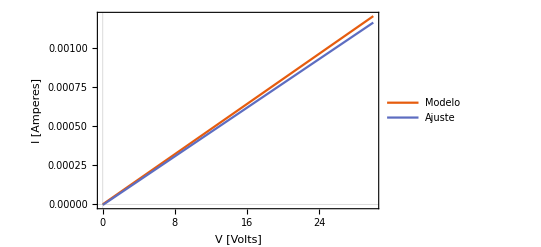

```mathematica
Plot[{V/24910,ajuste},{V,0,30},PlotTheme->"Scientific",FrameLabel->{"V [Volts]","I [Amperes]"},BaseStyle->FontSize->15,PlotLegends->{"Modelo","Ajuste"}]
```

Con el ajuste se puede estimar la resistencia equivalente del circuito. Primero se extrae el coeficiente de V

```mathematica
Coefficient[ajuste,V]
```

0.0000389016

Como la resistencia es el inverso del coeficiente que le pega a V entonces la resistencia es

```mathematica
1/Coefficient[ajuste,V]
```

25705.9

El método de ajuste que se utilizó presenta un problema a la hora de interpretar estadísticamente qué tan bueno es el ajuste. Para solventar este problema se puede utilizar un método de ajuste más sofisticado.

```mathematica
lm=LinearModelFit[datos,{1,V},V]
```

FittedModel[-3.94667×10^-6+0.0000389016 V]

Para recuperar el polinomio ajustado se hace

```mathematica
Normal[lm]
```

-3.94667×10^-6+0.0000389016 V

Con este tipo de ajuste se pueden obtener tablas que nos informan acerca de la bondad de ajuste del modelo.

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
V | 1 | 1.12365×10^-6 | 1.12365×10^-6 | 309396. | 1.22213×10^-19
Error | 8 | 2.90541×10^-11 | 3.63176×10^-12 |  | 
Total | 9 | 1.12368×10^-6 |  |  |

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -3.94667×10^-6 | 1.30185×10^-6 | -3.03158 | 0.0162703
V | 0.0000389016 | 6.99375×10^-8 | 556.234 | 1.22213×10^-19

Ejercicio

Se realizó un experimento en el cual se coloca un circuito con una resistencia con un área y longitud variables.

Se hace variar el área y se deja la longitud fija. La relación entre el área, longitud y resistencia está dada por

R = (ρ L)/A.

Los datos medidos con una resistencia con longitud L = 24 [cm] fueron los siguientes.

Obtener el valor de la resistividad ρ, y ver qué tan bueno es el ajuste.

## Análisis de modelos no lineales

En Mathematica también se pueden ajustar modelos no lineales, como exponenciales, logaritmos, leyes de potencias, etc.. A continuación se mostrará un ejemplo de análisis de frecuencia de palabras en un texto.
La ley de Zipf es una ley empírica que estipula que la frecuencia de las palabras en un texto es inversamente proporcional a su rango. Esto significa que la probabilidad de encontrar la n-ésima palabra más frecuente está dada por

P_n = c/n^α .

A continuación se hará un análisis de la frecuencia de las palabras en un texto.
Primero se importa el texto.

```mathematica
biblia = Import[NotebookDirectory[]<>"BIBLIA COMPLETA.txt"];
```

Se separa cada una de las palabras en una lista.

```mathematica
introList=StringSplit[biblia,Except[WordCharacter]..]
```

{LA,SANTA,BIBLIA,ANTIGUO,TESTAMENTO,VERSIÓN,DE,CASIODORO,DE,REINA,1569,REVISADA,POR,CIPRIANO,DE,VALERA,1602,OTRAS,REVISIONES,1862,1909,Y,1960,Parte,1,INCLUYE,LA,LEY,los,10,primeros,libros,del,AT,Gn,Ex,Lv,Nm,Dt,Jos,Jue,Rt,1,S,y,2,S,LIBRO,PRIMERO,DE,MOISÉS,755639,parte,del,libro,de,la,vida,y,de,la,santa,ciudad,y,de,las,cosas,que,están,escritas,en,este,libro,20,El,que,da,testimonio,de,estas,cosas,dice,Ciertamente,vengo,en,breve,Amén,sí,ven,Señor,Jesús,21,La,gracia,de,nuestro,Señor,Jesucristo,sea,con,todos,vosotros,Amén}
 |  |  |  |

Luego se eliminan los dígitos.

```mathematica
introList = StringDelete[introList,DigitCharacter]
```

{LA,SANTA,BIBLIA,ANTIGUO,TESTAMENTO,VERSIÓN,DE,CASIODORO,DE,REINA,,REVISADA,POR,CIPRIANO,DE,VALERA,,OTRAS,REVISIONES,,,Y,,Parte,,INCLUYE,LA,LEY,los,,primeros,libros,del,AT,Gn,Ex,Lv,Nm,Dt,Jos,Jue,Rt,,S,y,,S,LIBRO,PRIMERO,DE,MOISÉS,GÉNESIS,La,755635,quitará,su,parte,del,libro,de,la,vida,y,de,la,santa,ciudad,y,de,las,cosas,que,están,escritas,en,este,libro,,El,que,da,testimonio,de,estas,cosas,dice,Ciertamente,vengo,en,breve,Amén,sí,ven,Señor,Jesús,,La,gracia,de,nuestro,Señor,Jesucristo,sea,con,todos,vosotros,Amén}
 |  |  |  |

```mathematica
introList = DeleteCases[introList,""]
```

{LA,SANTA,BIBLIA,ANTIGUO,TESTAMENTO,VERSIÓN,DE,CASIODORO,DE,REINA,REVISADA,POR,CIPRIANO,DE,VALERA,OTRAS,REVISIONES,Y,Parte,INCLUYE,LA,LEY,los,primeros,libros,del,AT,Gn,Ex,Lv,Nm,Dt,Jos,Jue,Rt,S,y,S,LIBRO,PRIMERO,DE,MOISÉS,GÉNESIS,La,creación,Génesis,Génesis,En,el,719843,parte,del,libro,de,la,vida,y,de,la,santa,ciudad,y,de,las,cosas,que,están,escritas,en,este,libro,El,que,da,testimonio,de,estas,cosas,dice,Ciertamente,vengo,en,breve,Amén,sí,ven,Señor,Jesús,La,gracia,de,nuestro,Señor,Jesucristo,sea,con,todos,vosotros,Amén}
 |  |  |  |

Se convierten todas la palabras en minúsculas, se toma una muestra de 10000 palabras, se agrupan las palabras y se cuenta la frecuencia de cada palabra.

```mathematica
lowerIntroList=Map[ToLowerCase,introList];
lowerIntroList = lowerIntroList[[1;;10000]];
sortedIntroList=Sort[lowerIntroList];
wordFreq=Tally[sortedIntroList];

pltdata = Sort[wordFreq[[All,2]], Greater];
```

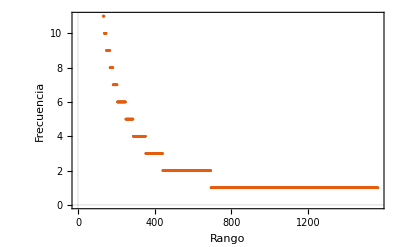

```mathematica
ListPlot[pltdata,ImageSize->400,PlotTheme->"Scientific",FrameLabel->{"Rango", "Frecuencia"},BaseStyle->FontSize->15]
```

Luego se ajusta un modelo no lineal.

{α→0.854558,c→913.589}

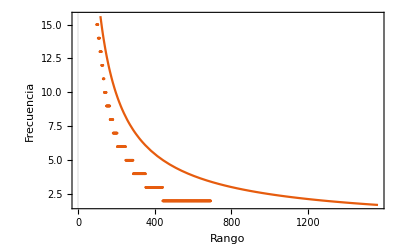

```mathematica
modelo = c/r^α;
fit = FindFit[pltdata ,modelo,{α,c},r]

modelf = Function[{r},Evaluate[modelo/.fit]];
Show[
Plot[modelf[r],{r,0,Length[pltdata]}, AxesLabel->{"Rango", "Frecuencia"},ImageSize->400,PlotTheme->"Scientific",FrameLabel->{"Rango", "Frecuencia"},BaseStyle->FontSize->14],
ListPlot[pltdata,PlotTheme->"Scientific"]
]
```

Ejercicio 1

Verificar la bondad de ajuste de este modelo. Para eso se tendrá que utilizar la función NonLinearModelFit en vez de FindFit.

Ejercicio 2

En un circuito construido con una resistencia y un capacitor

El voltaje respecto al tiempo  durante la carga del capacitor está dado por

V = ϵ e^(-t/RC).

Se realizó un experimento con un capacitor con capacitancia de 1000 μF y una resistencia de 46000 Ω. Si los datos medidos son

Estimar el voltaje de entrada ϵ.